# Quasinormal modes of Schwarzschild-like black holes

Author: Daniel del Corral Martínez
Contact: danidcmm@gmail.com

#### We begin by cleaning all variables we are going to use

```mathematica
Clear[A,B,rH,ϵ,l,β,M,γ,λ,V,v1,v2,v3,v4,v5,v6,v7,v8,v9,v10,v11,v12,V0,V1,V2,V3,V4,V5,V6,V7,V8,V9,V10,V11,V12,W1,W2,W3,W4,W5,W6,W7,W8,W9,W10,W11,W12,Λ,Ω,Φ,Θ,Ξ,σ3,σ4,σ5,σ6,QNM,DAB,VRW,sol,r0,ϵ,q,g,a1,a2,a3,a4,a5,a6,A1,A2,A3,A4,A5,A6,A7,A8,A9,A10,Λ,Ω,Φ,Θ,Ξ,T3,T4,T5,T6,T7,T8,T9,T10,T11,sol1,sol2,sol3,sol4,sol5,sol6,sol7,sol8,sol9,sol10,c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,b,c,d,f,h,l,m,n,p,r,V2,V3,V4,V5,V6,V7,V8,V9,V10,V11,V12,ζ3,ζ4,ζ5,ζ6,ζ7,ζ8,ζ9,ζ10,ζ11,ζ12,λ,ω,ϕ,θ,ξ]
```

### 1. Introduction

This notebook is aimed to the computation of quasinormal modes of non-singular black holes whose metric is Schwarzschild-like, i.e., it can be written in the following way:

ds^2=-A(r)dt^2+(B(r))^-1 dr^2+r^2 dΩ^2

In terms of these two functions A(r) and B(r), we can construct an effective potential [1], similar to the Regge-Wheeler potential for the Schwarzschild black hole. This potential appears on the differential equation that governs the small radial perturbations of the metric, given by:

(d^2 R)/dr^(*2)+Q(r)R=0,

where r^*is the tortoise coordinate. The complex oscillation frequencies of this radial solution, are what is called quasinormal modes. We use the WKB method in order to compute the quasinormal modes of the schwarzschild-like metric. This is derived in [2] up to 3th order and up to 6th order in [3]. Here we consider a 6th order WKB approximation. The basic idea of this method consist on dividing the potential in three regions. The central region, where the peak is (region II, r=r_0), and the asymptotic ones ( regions I and III, r=±∞). In regions I and III the solution is obtained considering an asymptotic, exponential function. Then, those solutions have to be matched to the solution in region II (interior solution), and this matching has to be done simultaneously for both regions (see [2] for details). Once this is complete, the following expression will allow us to compute the complex frequencies (quasinormal modes) of the perturbation:

ν + 1/2 = (-ik^(1/2)z_0^2)/(2ϵ)-ϵ Λ+ϵ^2 Ω+ϵ^3 Φ+ϵ^4 Θ+ϵ^5 Ξ

where the functions Λ,Ω,Φ,Θ,Ξ, depending only on the derivatives of the potential, will give us the differents corrections to each WKB order and are calculated in section 5.

As default, this notebook will compute the gravitational perturbations with angular momentum 2 (β=-3, l=2). If the reader wants to compute the quasinormal modes of another type of perturbation or another angular momentum it is necessary to change, in sec. 2, the definition of β and l.

Also, as default, this notebook is based on the Schwarzschild black hole. If the reader wants to compute the quasinormal modes of another black hole with the requirements described above it is necessary to change, in sec. 3, the components A(r) and B(r) of the metric. Remember they need to be normalized to r_H=1. Also, in sec.3 can be found two more examples of metrics. This time with corrections that arise from loop quantum gravity. They can be found in [1] and [4].

Once the metric and the type of perturbation is specified it is possible to evaluate the whole notebook and in sec. 8 the results are displayed. Depending on the complexity of the expressions it can take several minutes to complete. For the Schwarzschild black hole it should take less than one minute.

### 2. Type of perturbation

We start defining the type of perturbation we want to study with the β parameter: 
· β=-3 for gravitational
· β=0 for scalar 
· β=1 for electromagnetic
Also, we define the angular momentum, l, of the perturbation (remember that for l<2 the gravitational mode is non-radiative):

```mathematica
β=-3;
l=2;
```

### 3. Components of the metric

It is necessary for the metric to have spherical symmetry and the following shape:

ds^2=-A(r)dt^2+(B(r))^-1 dr^2+r^2 dΩ^2

In the Schwarzschild case, A(r) and B(r) are both given by:

```mathematica
A[r_]:=(1-1/r)
B[r_]:=(1-1/r)
```

Here are two more examples of metrics, which can be found in [1] and [4]:

```mathematica
Aaos[r_]:=r^(2δ)(1.-(1/r)^(1+δ))(1.+δ(1.+1/r))/(1.+δ)^3
Baos[r_]:=(1.-(1/r)^(1+δ))(1.+δ)/(1.+δ(1.+1/r))
Agop[y_]:=-(1-1/(y+x0)+Δ/(4π)1/((y+x0)^6(1/(y+x0)+1)^2))
Bgop[y_]:=(1+δx/(2. (y+x0)))^2/(1-1/(y+x0)+Δ/(4π)1/((y+x0)^6(1/(y+x0)+1)^2))
```

Typical values for the parameters describing this metrics are:

```mathematica
δ=0.01;
Δ=4.Pi Sqrt[3.] lpors^2;
δx=lpors;
x0=(Δ/(4.Pi))^(1./3.);
lpors=10^-4;
```

### 4. Derivation of the potential

The differential equation for the radial part of the perturbation is given by:

d^2/dr^(*2)Ψ(r^*)+Q(r)Ψ(r^*)=0
Q(r)=ω^2-V(r),

where ω is the frecuency of the perturbation and V(r) is the potential of the black hole. We can see that the derivatives and the radial part of the perturbation are both given in terms of the tortoise cordinate r^*, so it will be useful to obtain the function γ(r)=dr/dr^* which relates the radial and the tortoise coordinate. It is given by:

```mathematica
γ[r_]:=Sqrt[A[r]B[r]]
```

The effective potential for this metric can be obtained using the following formula (we define it already with the minus sing):

```mathematica
DAB[r_]:=D[A[r]B[r],r]//Evaluate;
V[r_]:=-(A[r]((l(l+1))/r^2)+β/(2r)DAB[r])//Factor//Simplify
```

In order to compare, we plot both the Schwarzschild and the case of study potential:

```mathematica
VSCH[r_]:=-(1-1/r)((l(l+1))/r^2+β/r^3)
```

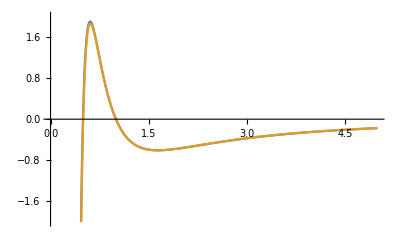

```mathematica
Plot[{V[r],VSCH[r]},{r,0,5},PlotRange-> {-2,2}]
```

### 5. WKB corrections functions

5.1. Definition of the functions q(t) and g(t) of the differential equation we want to solve:

First, we make the following change of variables: z=r-r_0, where r_0 is the position of the maximum of the potential Q(r). Then, the potential Q(z) is expanded up to 12th order in a Taylor series expansion (12th Taylor order is equivalent to 6th WKB order):

Q(z)=∑_(n=0)^∞ (Q_0^(n)z^n)/(n!)

where Q_0^(n) is the n-th derivative of the potential evaluated at the maximum. Now, we make the following changes:

k=Q_0^(2)/2          z_0^2=-(2 Q_0)/Q_0^(2)          ζ_n=2/Q_0^(2)(Q_0^(2)z^n)/(n!)

so that the potential now looks like this:

Q(z)=k (- z_0^2 + z^2+ ∑_(n=3)^∞ ζ_n z^n)

We can define a new variable t∝z/ϵ^(1/2) so that, when t→∞ as ϵ→0, this corresponds to the overlap between the interior solution in region II and the asymptotic WKB solutions in region I and III. The new variable is defined in this way :

t=((4k)^(1/4) e^(-iπ/4)z)/ϵ^(1/2)

We also redefine the coefficients z_0 and ζ_n as:

ν + 1/2 = (-ik^(1/2)z_0^2)/(2ϵ)-ϵ Λ+ϵ^2 Ω+ϵ^3 Φ+ϵ^4 Θ+ϵ^5 Ξ

(ζ̄)_n=(ζ_n/4[(4k)^-1 e^iπ])^((n-2)/4)

where the functions Λ,Ω,Φ,Θ,Ξ will give us the corrections to each of the WKB order. Now, we substitute this definitions for the potential in the differential equation for the radial component, and reagrupate in terms of ϵ, obtaining a new potential q(t):

(d^2 R)/dr^(*2)+q(r)R=0

where:

```mathematica
q[t_]:=ν+1/2-1/4 t^2-ϵ^(1/2)ζ3 t^3+ϵ (Λ-ζ4 t^4)-ϵ^(3/2)ζ5 t^5+ϵ^2(Ω-ζ6 t^6)-ϵ^(5/2)ζ7 t^7+ϵ^3 (Φ-ζ8 t^8)-ϵ^(7/2)ζ9 t^9+ϵ^4(Θ-ζ10 t^10)-ϵ^(9/2)ζ11 t^11+ϵ^5(Ξ-ζ12 t^12)//Evaluate
```

The solutions, without considering the terms in ϵ, are cylindrical functions D_ν(t) and D_(-ν-1)(it). We will therefore look for solutions of the type f(t)D_ν[ g(t) ] when considering the terms in ϵ. Choosing f=(dg/dt)^(1/2) and substituing in the differential equation (see [2] for details) we finally obtain this expression:

```mathematica
diffeq=g'[t]^4(ν+1/2-1/4 g[t]^2)+1/2 g'''[t]g'[t]-3/4 g''[t]^2-q[t] g'[t]^2;
```

Considering the polinomic form of the new potential q(t), we propose a similar form for the function g(t) in terms of ϵ and functions A_n(t):

```mathematica
g[t_]:=t+ϵ^(1/2)A1[t]+ϵ A2[t]+ϵ^(3/2)A3[t]+ϵ^2 A4[t]+ϵ^(5/2)A5[t]+ϵ^3 A6[t]+ϵ^(7/2)A7[t]+ϵ^4 A8[t]+ϵ^(9/2)A9[t]+ϵ^5 A10[t]//Evaluate
```

5.2. Derivation of the differential equations for each of the A_n(t):

Let us now expand the differential equation and reagrupate in terms of ϵ^(1/2). We will then solve for each of the powers of ϵ^(1/2). We begin with the lowest one, and this will result in a differential equation for the coefficient A1(t), which we will call a1(t):

```mathematica
a1[t_]:=Coefficient[Collect[diffeq,ϵ^(1/2)],ϵ,1/2]//Simplify //Evaluate
```

We clear the term ζ3 t^3, which will appear below, and call it T3:

```mathematica
T3=-a1[t]+ζ3 t^3//Simplify;
```

Let us move forward to the next order, ϵ . We can see that it appears the term T3, so substituing it, we can obtain now a differential equation for the coefficient A1(t) and A2(t) :

```mathematica
a2[t_]:=Coefficient[Collect[diffeq,ϵ^(1/2)],ϵ,1]/. {ζ3 t^3-> (T3)}//Simplify//Evaluate
```

We do the same as before but now with the term ζ4 t^4, and call it T4:

```mathematica
T4=-a2[t]+ζ4 t^4//Simplify;
```

The next order, ϵ^(3/2), substituing T3 and T4:

```mathematica
a3[t_]:=Coefficient[Collect[diffeq,ϵ^(1/2)],ϵ,3/2]/. {ζ3 t^3-> (T3),ζ4 t^4-> (T4)}//Simplify//Evaluate
```

We clear T5:

```mathematica
T5=-a3[t]+ζ5 t^5//Simplify;
```

Next order, ϵ^2. The procedure is the same:

```mathematica
a4[t_]:=Coefficient[Collect[diffeq,ϵ^(1/2)],ϵ,2]/. {ζ3 t^3-> (T3),ζ4 t^4-> (T4),ζ5 t^5-> (T5)}//Simplify//Evaluate
```

We clear T6:

```mathematica
T6=-a4[t]+ζ6 t^6//Simplify;
```

Next order, ϵ^(5/2):

```mathematica
a5[t_]:=Coefficient[Collect[diffeq,ϵ^(1/2)],ϵ,5/2]/. {ζ3 t^3-> (T3),ζ4 t^4-> (T4),ζ5 t^5-> (T5),ζ6 t^6-> (T6)}//Simplify//Evaluate
```

We clear T7

```mathematica
T7=-a5[t]+ζ7 t^7//Simplify;
```

Pasamos al siguiente orden ϵ^3:

```mathematica
a6[t_]:=Coefficient[Collect[diffeq,ϵ^(1/2)],ϵ,3]/. {ζ3 t^3-> (T3),ζ4 t^4-> (T4),ζ5 t^5-> (T5),ζ6 t^6-> (T6),ζ7 t^7-> (T7)}//Simplify//Evaluate
```

We clear T8:

```mathematica
T8=-a6[t]+ζ8 t^8//Simplify;
```

Next order, ϵ^(7/2):

```mathematica
a7[t_]:=Coefficient[Collect[diffeq,ϵ^(1/2)],ϵ,7/2]/. {ζ3 t^3-> (T3),ζ4 t^4-> (T4),ζ5 t^5-> (T5),ζ6 t^6-> (T6),ζ7 t^7-> (T7),ζ8 t^8-> (T8)}//Simplify//Evaluate
```

We clear T9:

```mathematica
T9=-a7[t]+ζ9 t^9//Simplify;
```

Next order, ϵ^4:

```mathematica
a8[t_]:=Coefficient[Collect[diffeq,ϵ^(1/2)],ϵ,4]/. {ζ3 t^3-> (T3),ζ4 t^4-> (T4),ζ5 t^5-> (T5),ζ6 t^6-> (T6),ζ7 t^7-> (T7),ζ8 t^8-> (T8),ζ9 t^9-> (T9)}//Simplify //Evaluate
```

We clear T10:

```mathematica
T10=-a8[t]+ζ10 t^10//Simplify;
```

Next order, ϵ^(9/2):

```mathematica
a9[t_]:=Coefficient[Collect[diffeq,ϵ^(1/2)],ϵ,9/2]/. {ζ3 t^3-> (T3),ζ4 t^4-> (T4),ζ5 t^5-> (T5),ζ6 t^6-> (T6),ζ7 t^7-> (T7),ζ8 t^8-> (T8),ζ9 t^9-> (T9),ζ10 t^10-> (T10)}//Simplify //Evaluate
```

We clear T11:

```mathematica
T11=-a9[t]+ζ11 t^11//Simplify;
```

Finally, the order ϵ^5:

```mathematica
a10[t_]:=Coefficient[Collect[diffeq,ϵ^(1/2)],ϵ,5]/. {bζ3 t^3-> (T3),ζ4 t^4-> (T4),ζ5 t^5-> (T5),ζ6 t^6-> (T6),ζ7 t^7-> (T7),ζ8 t^8-> (T8),ζ9 t^9-> (T9),ζ10 t^10-> (T10),ζ11 t^11-> (T11)}//Simplify //Evaluate
```

5.3. Proposal of a polinomic form for each A_n(t):

We already have all the differential equations needed to solve the An(t) coefficients. If we now look both the homogeneous and inhomogeneous terms of the differential equations, it is possible to propose the following form for the coefficients:

```mathematica
A1[t_]:=c1[2]+c1[1]t+c1[0] t^2+c1[-1] t^3
A2[t_]:=c2[2]+c2[1]t+c2[0] t^2+c2[-1] t^3+c2[-2] t^4
A3[t_]:=c3[2]+c3[1]t+c3[0] t^2+c3[-1] t^3+c3[-2] t^4+c3[-3] t^5
A4[t_]:=c4[2]+c4[1]t+c4[0] t^2+c4[-1] t^3+c4[-2] t^4+c4[-3] t^5+c4[-4] t^6
A5[t_]:=c5[2]+c5[1]t+c5[0] t^2+c5[-1] t^3+c5[-2] t^4+c5[-3] t^5+c5[-4] t^6+c5[-5] t^7
A6[t_]:=c6[2]+c6[1]t+c6[0] t^2+c6[-1] t^3+c6[-2] t^4+c6[-3] t^5+c6[-4] t^6+c6[-5] t^7+c6[-6] t^8
A7[t_]:=c7[2]+c7[1]t+c7[0] t^2+c7[-1] t^3+c7[-2] t^4+c7[-3] t^5+c7[-4] t^6+c7[-5] t^7+c7[-6] t^8+c7[-7] t^9
A8[t_]:=c8[2]+c8[1]t+c8[0] t^2+c8[-1] t^3+c8[-2] t^4+c8[-3] t^5+c8[-4] t^6+c8[-5] t^7+c8[-6] t^8+c8[-7] t^9+c8[-8] t^10
A9[t_]:=c9[2]+c9[1]t+c9[0] t^2+c9[-1] t^3+c9[-2] t^4+c9[-3] t^5+c9[-4] t^6+c9[-5] t^7+c9[-6] t^8+c9[-7] t^9+c9[-8] t^10+c9[-9] t^11
A10[t_]:=c10[2]+c10[1]t+c10[0] t^2+c10[-1] t^3+c10[-2] t^4+c10[-3] t^5+c10[-4] t^6+c10[-5] t^7+c10[-6] t^8+c10[-7] t^9+c10[-8] t^10+c10[-9] t^11+c10[-10] t^12
```

5.4. Derivation of the coefficients of the polinomic form of A_n(t) and the corrections to each WKB order (Λ,Ω,Φ,Θ,Ξ):

We therefore solve now for each coefficient An(t). We begin with A1(t), so we need to solve a1(t). The procedure, as in every other order, will be to isolate each of the powers of t in a1(t) and equate to each coefficient cn(t) of A1(t). The system results to be determined:

```mathematica
sol1=Solve[ParallelTable[Coefficient[a1[t],t,i]==0,{i,0,4}]//Evaluate,{c1[-1],c1[0],c1[1],c1[2]}];
```

```mathematica
Table[c1[i-2]=sol1[[1,i,2]],{i,1,4}];
```

If we repeat this for a2(t), we will find that the system is overdetermined. However, the correction Λ appears and the system is now determined. This is the way to calculate each of the corrections for the WKB order:

```mathematica
sol2=Solve[ParallelTable[Coefficient[a2[t],t,i]==0,{i,0,5}]//Evaluate,{c2[-2],c2[-1],c2[0],c2[1],c2[2],Λ}];
```

```mathematica
Table[c2[i-2]=sol2[[1,i+1,2]],{i,0,4}];
```

```mathematica
λ=sol2[[1,6,2]];
```

The same now for the rest of the differential equations an(t):

```mathematica
sol3=Solve[ParallelTable[Coefficient[a3[t],t,i]==0,{i,0,6}]//Evaluate,{c3[-3],c3[-2],c3[-1],c3[0],c3[1],c3[2]}];
```

```mathematica
Table[c3[i-3]=sol3[[1,i+1,2]],{i,0,5}];
```

```mathematica
sol4=Solve[ParallelTable[Coefficient[a4[t],t,i]==0,{i,0,7}]//Evaluate,{c4[-4],c4[-3],c4[-2],c4[-1],c4[0],c4[1],c4[2],Ω}];
```

```mathematica
Table[c4[i-4]=sol4[[1,i+1,2]],{i,0,6}];
```

```mathematica
ω=sol4[[1,8,2]];
```

```mathematica
sol5=Solve[ParallelTable[Coefficient[a5[t],t,i]==0,{i,0,8}]//Evaluate,{c5[-5],c5[-4],c5[-3],c5[-2],c5[-1],c5[0],c5[1],c5[2]}];
```

```mathematica
Table[c5[i-5]=sol5[[1,i+1,2]],{i,0,7}];
```

```mathematica
sol6=Solve[ParallelTable[Coefficient[a6[t],t,i]==0,{i,0,9}],{c6[-6],c6[-5],c6[-4],c6[-3],c6[-2],c6[-1],c6[0],c6[1],c6[2],Φ}];
```

```mathematica
Table[c6[i-6]=sol6[[1,i+1,2]],{i,0,8}];
```

```mathematica
ϕ=sol6[[1,10,2]];
```

```mathematica
sol7=Solve[ParallelTable[Coefficient[a7[t],t,i]==0,{i,0,10}],{c7[-7],c7[-6],c7[-5],c7[-4],c7[-3],c7[-2],c7[-1],c7[0],c7[1],c7[2]}];
```

```mathematica
Table[c7[i-7]=sol7[[1,i+1,2]],{i,0,9}];
```

```mathematica
sol8=Solve[ParallelTable[Coefficient[a8[t],t,i]==0,{i,0,11}],{c8[-8],c8[-7],c8[-6],c8[-5],c8[-4],c8[-3],c8[-2],c8[-1],c8[0],c8[1],c8[2],Θ}];
```

```mathematica
Table[c8[i-8]=sol8[[1,i+1,2]],{i,0,10}];
```

```mathematica
θ=sol8[[1,12,2]];
```

```mathematica
sol9=Solve[ParallelTable[Coefficient[a9[t],t,i]==0,{i,0,12}],{c9[-9],c9[-8],c9[-7],c9[-6],c9[-5],c9[-4],c9[-3],c9[-2],c9[-1],c9[0],c9[1],c9[2]}];
```

```mathematica
Table[c9[i-9]=sol9[[1,i+1,2]],{i,0,11}];
```

```mathematica
sol10=Solve[ParallelTable[Coefficient[a10[t],t,i]==0,{i,0,13}],{c10[-10],c10[-9],c10[-8],c10[-7],c10[-6],c10[-5],c10[-4],c10[-3],c10[-2],c10[-1],c10[0],c10[1],c10[2],Ξ}];
```

```mathematica
Table[c10[i-10]=sol10[[1,i+1,2]],{i,0,12}];
```

```mathematica
ξ=sol10[[1,14,2]];
```

5.5. Expression of the corrections Λ,Ω,Φ,Θ,Ξ as a function of the derivatives of the black hole:

We already have the WKB corrections functions Λ,Ω,Φ,Θ,Ξ but in terms of ζn. Let us now define this ζn coefficients in terms of the derivatives, evaluated in the maximum, in order to calculate the corrections functions and therefore the quasinormal modes:

```mathematica
ζ3= 2/Factorial[3] V3/V2 1/4(2V2)^(-1/4)E^(1 I Pi/4);ζ4= 2/Factorial[4] V4/V2 1/4(2V2)^(-2/4)E^(2 I Pi/4);ζ5= 2/Factorial[5] V5/V2 1/4(2V2)^(-3/4)E^(3 I Pi/4);
ζ6= 2/Factorial[6] V6/V2 1/4(2V2)^(-4/4)E^(4 I Pi/4);
ζ7= 2/Factorial[7] V7/V2 1/4(2V2)^(-5/4)E^(5 I Pi/4);
ζ8= 2/Factorial[8] V8/V2 1/4(2V2)^(-6/4)E^(6 I Pi/4);
ζ9= 2/Factorial[9] V9/V2 1/4(2V2)^(-7/4)E^(7 I Pi/4);
ζ10= 2/Factorial[10] V10/V2 1/4(2V2)^(-8/4)E^(8 I Pi/4);ζ11= 2/Factorial[11] V11/V2 1/4(2V2)^(-9/4)E^(9 I Pi/4);ζ12= 2/Factorial[12] V12/V2 1/4(2V2)^(-10/4)E^(10 I Pi/4);
```

Finally, we will perform the following change of notation in order to be coherent with [2], we will change ν by α-1/2:

```mathematica
Λ[α_]:=λ/.ν-> (α-1/2)//Simplify
```

```mathematica
Ω[α_]:=ω/. ν-> (α-1/2)//Simplify
```

```mathematica
Φ[α_]:=ϕ/. ν-> (α-1/2)//Simplify
```

```mathematica
Θ[α_]:=θ/. ν-> (α-1/2)//Simplify
```

```mathematica
Ξ[α_]:=ξ/. ν-> (α-1/2)//Simplify
```

### 6. Derivatives

Now, we compute the derivatives of the potential making use of the γ(r)=dr^*/dr function. For 6th order we have to compute until the 12th derivative:

```mathematica
γ[r]V'[r]//Factor//Simplify;
```

```mathematica
v1[r_]=%;
```

```mathematica
γ[r]D[%%,r]//Factor//Simplify;
```

```mathematica
v2[r_]=%;
```

```mathematica
γ[r]D[%%,r]//Factor//Simplify;
```

```mathematica
v3[r_]=%;
```

```mathematica
γ[r]D[%%,r]//Factor//Simplify;
```

```mathematica
v4[r_]=%;
```

```mathematica
γ[r]D[%%,r]//Factor//Simplify;
```

```mathematica
v5[r_]=%;
```

```mathematica
γ[r]D[%%,r]//Factor//Simplify;
```

```mathematica
v6[r_]=%;
```

```mathematica
γ[r]D[%%,r]//Factor//Simplify;
```

```mathematica
v7[r_]=%;
```

```mathematica
γ[r]D[%%,r]//Factor//Simplify;
```

```mathematica
v8[r_]=%;
```

```mathematica
γ[r]D[%%,r]//Factor//Simplify;
```

```mathematica
v9[r_]=%;
```

```mathematica
γ[r]D[%%,r]//Factor//Simplify;
```

```mathematica
v10[r_]=%;
```

```mathematica
γ[r]D[%,r]//Factor//Simplify;
```

```mathematica
v11[r_]=%;
```

```mathematica
γ[r]D[%,r]//Factor//Simplify;
```

```mathematica
v12[r_]=%;
```

We calculate the minimum of the potential:

```mathematica
sol=NSolve[{V'[r]==0,V''[r]>0,r>1.},r];
```

```mathematica
r0=r/. sol[[1]];
```

And evaluate the derivatives at this point:

```mathematica
V0=V[r0]//N;
V1=v1[r0]//N;
V2=v2[r0]//N;
V3=v3[r0]//N;
V4=v4[r0]//N;
V5=v5[r0]//N;
V6=v6[r0]//N;
```

```mathematica
V7=v7[r0]//N;
```

```mathematica
V8=v8[r0]//N;
```

```mathematica
V9=v9[r0]//N;
```

```mathematica
V10=v10[r0]//N;
```

```mathematica
V11=v11[r0]//N;
```

```mathematica
V12=v12[r0]//N;
```

### 7. Calculation of the quasinormal modes

And the equations that allow us to compute the quasinormal modes are given, at each WKB order, by:

```mathematica
σ1[α_]:=Sqrt[-V0-ⅈ √(2V2)(α)]
```

```mathematica
σ2[α_]:=Sqrt[-V0-ⅈ √(2V2)(α+ Λ[α])]
```

```mathematica
σ3[α_]:=Sqrt[-V0-ⅈ √(2V2)(α+ Λ[α]+ Ω[α])]
```

```mathematica
σ4[α_]:=Sqrt[-V0-ⅈ √(2V2) (α+ Λ[α]+ Ω[α]+Φ[α])]
```

```mathematica
σ5[α_]:=Sqrt[-V0-ⅈ √(2V2) (α+ Λ[α]+ Ω[α]+Φ[α]+Θ[α])]
```

```mathematica
σ6[α_]:=Sqrt[-V0-ⅈ √(2V2) (α+Λ[α]+Ω[α]+Φ[α]+Θ[α]+Ξ[α])]
```

Let us finally compute the quasinormal modes:

```mathematica
QNM=MapThread[Prepend,{Prepend[{Round[Table[σ1[n+1/2],{n,0,2}]//N,0.0001],Round[Table[σ2[n+1/2],{n,0,2}]//N,0.0001],Round[Table[σ3[n+1/2],{n,0,2}]//N,0.0001],Round[Table[σ4[n+1/2],{n,0,2}]//N,0.0001],Round[Table[σ5[n+1/2],{n,0,2}]//N,0.0001],Round[Table[σ6[n+1/2],{n,0,2}]//N,0.0001]},{"n=0","n=1","n=2"}],{"","1st","2nd","3rd","4th","5th","6th"}}];
```

### 8. Results

In this table the quasinormal modes of the black hole are given for the first three overtones (n=0,1,2) and for each WKB order

```mathematica
Insert[Grid[QNM],{Background->{{GrayLevel[0.7],{White}},{GrayLevel[0.7],{White}}},Dividers->{Black,{2->Black}},Frame->True,Spacings->{5,{2,{2},2}}},2]
```

| n=0 | n=1 | n=2
1st | 0.7982-0.1764 ⅈ | 0.9071-0.4657 ⅈ | 1.0342-0.6808 ⅈ
2nd | 0.7493-0.1879 ⅈ | 0.7216-0.5855 ⅈ | 0.7007-1.0048 ⅈ
3rd | 0.7469-0.1783 ⅈ | 0.6926-0.5493 ⅈ | 0.6062-0.9413 ⅈ
4th | 0.7477-0.1781 ⅈ | 0.6931-0.5489 ⅈ | 0.5963-0.9569 ⅈ
5th | 0.7476-0.1777 ⅈ | 0.692-0.5474 ⅈ | 0.5959-0.9567 ⅈ
6th | 0.7478-0.1776 ⅈ | 0.6932-0.5464 ⅈ | 0.5975-0.9542 ⅈ

In this graphic we show how does the real and imaginary part of the first overtone change with the WKB order:

```mathematica
ListPlot[{{Re[σ1[1/2]],Re[σ2[1/2]],Re[σ3[1/2]],Re[σ4[1/2]],Re[σ5[1/2]],Re[σ6[1/2]]},{Im[σ1[1/2]],Im[σ2[1/2]],Im[σ3[1/2]],Im[σ4[1/2]],Im[σ5[1/2]],Im[σ6[1/2]]}},PlotRange-> Automatic,PlotMarkers->{Automatic, Medium},Joined->True,AxesLabel-> {"WKB Order"},DataRange-> {1,6},Ticks->{{1,2,3,4,5,6}, Automatic},PlotLegends->Placed[{"Re(ω)","Im(ω)"},{1,0.55}]]
```

-Graphics-

In this graphic we show how does the real and imaginary part of the third overtone change with the WKB order:

```mathematica
ListPlot[{{Re[σ1[2+1/2]],Re[σ2[2+1/2]],Re[σ3[2+1/2]],Re[σ4[2+1/2]],Re[σ5[2+1/2]],Re[σ6[2+1/2]]},{Im[σ1[2+1/2]],Im[σ2[2+1/2]],Im[σ3[2+1/2]],Im[σ4[2+1/2]],Im[σ5[2+1/2]],Im[σ6[2+1/2]]}},PlotRange-> Automatic,PlotMarkers->{Automatic, Medium},Joined->True,AxesLabel-> {"WKB Order"},DataRange-> {1,6},Ticks->{{1,2,3,4,5,6}, Automatic},PlotLegends->Placed[{"Re(ω)","Im(ω)"},{1,0.3}]]
```

-Graphics-

### 9. References

[1] R. G. Daghigh, M. D. Green and G. Kunstatter, “Scalar Perturbations and Stability of a Loop Quantum Corrected Kruskal Black Hole”, Phys. Rev. D 103 (2021) no.8, 084031.

[2] S. Iyer and C. M. Will, “Black Hole Normal Modes: A {WKB} Approach. 1. Foundations and Application of a Higher Order {WKB} Analysis of Potential Barrier Scattering”, Phys. Rev. D 35 (1987), 3621.

[3] R. A. Konoplya, “Quasinormal behavior of the D-dimensional Schwarzschild black hole and higher order WKB approach,“ Phys. Rev. D 68 (2003), 024018.

[4] R. Gambini, J. Olmedo and J. Pullin,“Spherically symmetric loop quantum gravity: analysis of improved dynamics,” Class. Quant. Grav. 37 (2020) no.20, 205012.